# Quantum geometry and ferromagnetic fluctuations at the monkey saddle of biased bilayer graphene

## Working notebook: every figure of my report, computed from the four-band model

Rajat Shuvra Saha — School of Physical Sciences, NISER

At a critical interlayer bias V_c ≃ 40  meV the three van Hove saddles of the lowest conduction band of Bernal bilayer graphene merge into one monkey saddle, a higher-order van Hove singularity. Following Kitamura, Daido and Yanase, this notebook asks whether the quantum geometry of that band favours ferromagnetic fluctuations. The quantity to watch is the generalized electric susceptibility (GES) χ_e, the q^2 curvature of the bare susceptibility, split into a geometric part χ_geom and an effective-mass part χ_mass.

Plan of the talk

1. Model: the four-band Hamiltonian

2. The monkey saddle: shape, critical points, the three saddle phases (Figs. 1, 2, Table I)

3. Quantum geometry of the critical band (Table II)

4. Generalized electric susceptibility: formulas and numerical method

5. Results: chemical potential, temperature, finite q, phase diagram (Figs. 3 to 7)

6. Benchmark: the singular saddle point of Kitamura et al. (Fig. 8)

7. Conclusions

How to run. Evaluate the cells from top to bottom (Evaluation > Evaluate Notebook). Sections 1 to 3 are instant. The band data of Section 4 and the finite-q scan of Section 5.4 are the slow cells; each one says so in a comment. Units: energies in eV, momenta in nm^-1; μ and T are quoted in meV, with μ measured from V/2.

```mathematica
ClearAll["Global`*"]

cBlue = RGBColor[0.227, 0.431, 0.647];
cBrown = RGBColor[0.545, 0.271, 0.075];
cOrange = RGBColor[0.851, 0.478, 0.110];
biasColors = {cBlue, cBrown, cOrange};
```

## 1. Model

Four-band continuum Hamiltonian of Bernal bilayer graphene near valley K, in the basis (A_1, B_1, A_2, B_2), with interlayer bias V (McCann and Koshino):

H(k) = (V/2 | v π^† | 0 | v_3 π
v π | V/2 | γ_1 | 0
0 | γ_1 | -V/2 | v π^†
v_3 π^† | 0 | v π | -V/2) ,    π = k_x + i k_y

Parameters: v = 0.658  eV nm, γ_1 = 0.40  eV, v_3 = 0.1 v. The Hamiltonian is linear in k, so the velocity matrices ∂_x H and ∂_y H are constant. Every band derivative used later is then an exact finite sum over the four states.

```mathematica
v = 0.658;  g1 = 0.40;  v3 = 0.1 v;

(* constant velocity matrices dH/dkx and dH/dky *)
dHx = {{0, v, 0, v3}, {v, 0, 0, 0}, {0, 0, 0, v}, {v3, 0, v, 0}};
dHy = {{0, -I v, 0, I v3}, {I v, 0, 0, 0}, {0, 0, 0, -I v}, {-I v3, 0, I v, 0}};

h0[V_] := {{V/2, 0, 0, 0}, {0, V/2, g1, 0}, {0, g1, -V/2, 0}, {0, 0, 0, -V/2}};
ham[kx_, ky_, V_] := h0[V] + kx dHx + ky dHy;

MatrixForm[ham[kx, ky, V]]
```

(V/2 | 0.658 kx-(0.+0.658 ⅈ) ky | 0 | 0.0658 kx+(0.+0.0658 ⅈ) ky
0.658 kx+(0.+0.658 ⅈ) ky | V/2 | 0.4 | 0
0 | 0.4 | -V/2 | 0.658 kx-(0.+0.658 ⅈ) ky
0.0658 kx-(0.+0.0658 ⅈ) ky | 0 | 0.658 kx+(0.+0.658 ⅈ) ky | -V/2)

Eigenvalues come out of Eigensystem in no useful order, so we sort them once and for all. bands returns the four energies in ascending order together with the matching eigenvectors (one per row). Band 3 is the lowest conduction band; at k = 0 it is the pure A_1 orbital at energy V/2.

```mathematica
bands[kx_, ky_, V_] := Module[{vals, vecs, ord},
  {vals, vecs} = Eigensystem[ham[kx, ky, V]];
  ord = Ordering[vals];
  {vals[[ord]], vecs[[ord]]}]

band[n_, kx_?NumericQ, ky_?NumericQ, V_] := bands[kx, ky, V][[1, n]]
eps3[kx_, ky_, V_] := band[3, kx, ky, V]
```

```mathematica
(* characteristic scales *)
Vc = g1 v3/v;                    (* critical bias *)
A3 = 2 v^3/g1^2;                 (* cubic coefficient A *)
B4 = v^5/(g1^3 v3);              (* quartic coefficient B *)
ks = A3/B4;  Es = A3^4/B4^3;     (* crossover scales k* and E* *)

{1000 Vc, ks, 1000 Es}           (* 40 meV, 0.122 nm^-1, 6.40 meV *)
```

{40.,0.121581,6.4}

The four bands along k_x at V = V_c, and a close-up of band 3 for three biases. In the close-up the band bottom at k = 0 flattens at V_c and then turns into a maximum.

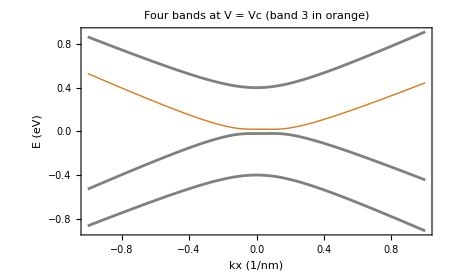

```mathematica
Plot[{band[1, k, 0, Vc], band[2, k, 0, Vc], band[3, k, 0, Vc], band[4, k, 0, Vc]}, {k, -1, 1},
 PlotStyle -> {Gray, Gray, Directive[cOrange, Thick], Gray},
 Frame -> True, FrameLabel -> {"kx (1/nm)", "E (eV)"},
 PlotLabel -> "Four bands at V = Vc (band 3 in orange)", ImageSize -> 450]
```

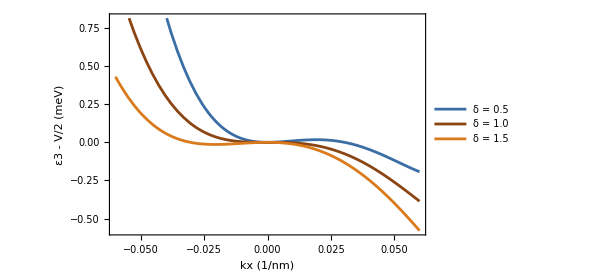

```mathematica
Plot[{1000 (eps3[k, 0, 0.5 Vc] - 0.5 Vc/2), 1000 (eps3[k, 0, Vc] - Vc/2),
  1000 (eps3[k, 0, 1.5 Vc] - 1.5 Vc/2)}, {k, -0.06, 0.06},
 PlotStyle -> biasColors, Frame -> True,
 FrameLabel -> {"kx (1/nm)", "ε3 - V/2 (meV)"},
 PlotLegends -> {"δ = 0.5", "δ = 1.0", "δ = 1.5"}, ImageSize -> 450]
```

## 2. The monkey saddle

### 2.1 Effective dispersion

Eliminating the dimer orbitals (B_1, A_2) gives, to leading order,

ε_3(k) - V/2 ≃ α(V) k^2 - A k^3 cos 3φ + B k^4 ,    α(V) = v_3^2/V - (v^2 V)/γ_1^2

The k^2 coefficient is a competition: direct trigonal-warping hopping to B_2 pushes the band up, virtual hopping through the dimer pushes it down. The two cancel at the critical bias, where the cubic term fixes the shape:

V_c = (γ_1 v_3)/v = 40  meV ,    A = (2 v^3)/γ_1^2 ,    B = v^5/(γ_1^3 v_3) ,    k_* = A/B = 0.122 nm^-1 ,    E_* = A^4/B^3 = 6.40  meV

Throughout, δ ≡ V/V_c. Quick check of α(V) against exact diagonalisation: along φ = π/6 the cubic term vanishes, so (ε_3 - V/2)/k^2 at small k is the k^2 coefficient.

```mathematica
alpha[V_] := v3^2/V - v^2 V/g1^2

kt = 0.001;
TableForm[
 Table[{del, (eps3[kt Cos[Pi/6], kt Sin[Pi/6], del Vc] - del Vc/2)/kt^2, alpha[del Vc]},
  {del, {0.5, 0.8, 1.2, 1.5}}],
 TableHeadings -> {None, {"δ", "k^2 coefficient, exact", "α(V), formula"}}]
```

δ | k^2 coefficient, exact | α(V), formula
0.5 | 0.162418 | 0.162362
0.8 | 0.0487447 | 0.0487085
1.2 | -0.0396638 | -0.0396884
1.5 | -0.0901809 | -0.0902008

### 2.2 The shape of the monkey saddle (Fig. 1)

At V = V_c the surface rises along three directions and falls along the three in between. The Hessian vanishes at the centre, so the density of states diverges as |E - E_c|^(-1/3) instead of logarithmically. First the ideal cubic form -k^3 cos 3φ = -(x^3 - 3 x y^2), then the actual band 3 of the four-band model in units of k_* and E_*.

```mathematica
Plot3D[-(x^3 - 3 x y^2), {x, -0.5, 0.5}, {y, -0.5, 0.5}]
```

```mathematica
Plot3D[(eps3[x ks, y ks, Vc] - Vc/2)/Es, {x, -0.5, 0.5}, {y, -0.5, 0.5},
 AxesLabel -> {"kx/k*", "ky/k*", "(ε3 - Vc/2)/E*"}, PlotPoints -> 30]
```

-Graphics3D-

### 2.3 Critical points (Table I)

Because H(k_x, -k_y) = H(k_x, k_y)^*, band 3 is even in k_y. Every zero of the slope ∂ ε_3/∂ k_x on the k_x axis is therefore a true critical point. The negative axis is the φ = π/3 mirror line up to a C_3 rotation, so one scan of the axis finds everything. The slope is the Hellmann–Feynman expectation value ⟨ 3| ∂_x H |3 ⟩; sign changes are bracketed on a grid and refined by bisection. k = 0 is always a critical point by symmetry.

```mathematica
slope[k_?NumericQ, V_] := Module[{u = bands[k, 0, V][[2, 3]]},
  Re[Conjugate[u].dHx.u]]

(* zero of the slope between a0 and b0 by bisection *)
bisect[V_, a0_, b0_] := Module[{a = a0, b = b0, c},
  Do[c = (a + b)/2;
   If[slope[a, V] slope[c, V] <= 0, b = c, a = c], {40}];
  (a + b)/2]

criticalK[V_] := Module[{kk, s, roots = {}},
  kk = Table[(-1.605 + 0.01 i) ks, {i, 0, 320}];
  s = Table[slope[k, V], {k, kk}];
  Do[If[s[[i]] s[[i + 1]] < 0, AppendTo[roots, bisect[V, kk[[i]], kk[[i + 1]]]]],
   {i, Length[kk] - 1}];
  Prepend[Select[roots, Abs[#] > 0.001 ks &], 0.]]

criticalK[0.5 Vc]/ks
```

{0.,0.158368,0.589789}

Each point is classified by the exact Hessian of band 3. For a Hamiltonian linear in k:

∂_μ ∂_ν ε_n = ∑_(m ≠ n) (2 Re[ v_nm^μ v_mn^ν ])/(ε_n - ε_m) ,    v_nm^μ = ⟨ n| ∂_μ H |m ⟩

```mathematica
hessian[kx_, ky_, V_] := Module[{e, U, vx, vy, hxx = 0, hyy = 0, hxy = 0},
  {e, U} = bands[kx, ky, V];
  vx = Conjugate[U].dHx.Transpose[U];      (* vx[[n, m]] = <n| dH/dkx |m> *)
  vy = Conjugate[U].dHy.Transpose[U];
  Do[If[m != 3,
    hxx += 2 Abs[vx[[3, m]]]^2/(e[[3]] - e[[m]]);
    hyy += 2 Abs[vy[[3, m]]]^2/(e[[3]] - e[[m]]);
    hxy += 2 Re[vx[[3, m]] vy[[m, 3]]]/(e[[3]] - e[[m]])], {m, 4}];
  {{hxx, hxy}, {hxy, hyy}}]

kind[h_] := Module[{ev = Eigenvalues[h]},
  Which[Max[Abs[ev]] < 10^-6, "monkey saddle",
   Min[ev] > 0, "minimum",
   Max[ev] < 0, "maximum",
   True, "saddle"]]
```

```mathematica
tableI = Flatten[
   Table[
    Table[{del, k/ks, 1000 (eps3[k, 0, del Vc] - del Vc/2),
      Chop[Sort[Eigenvalues[hessian[k, 0, del Vc]]], 10^-8], kind[hessian[k, 0, del Vc]]},
     {k, criticalK[del Vc]}],
    {del, {0.5, 1.0, 1.5}}], 1];

Grid[Prepend[tableI, {"δ", "kx/k*", "E - V/2 (meV)", "Hessian eigenvalues (eV nm^2)", "type"}],
 Frame -> All, Alignment -> Left]
```

δ | kx/k* | E - V/2 (meV) | Hessian eigenvalues (eV nm^2) | type
0.5 | 0. | 0. | Eigenvalues[hessian[0,0,0.02]] | kind[hessian[0.,0,0.02]]
0.5 | 0.158368 | 0.0173537 | Eigenvalues[hessian[0.0192544,0,0.02]] | kind[hessian[0.0192544,0,0.02]]
0.5 | 0.589789 | -0.238631 | Eigenvalues[hessian[0.0717069,0,0.02]] | kind[hessian[0.0717069,0,0.02]]
1. | 0. | 0. | Eigenvalues[hessian[0,0,0.04]] | kind[hessian[0.,0,0.04]]
1. | 0.744551 | -0.656677 | Eigenvalues[hessian[0.0905229,0,0.04]] | kind[hessian[0.0905229,0,0.04]]
1.5 | 0. | 0. | Eigenvalues[hessian[0,0,0.06]] | kind[hessian[0.,0,0.06]]
1.5 | -0.169742 | -0.0139785 | Eigenvalues[hessian[-0.0206373,0,0.06]] | kind[hessian[-0.0206373,0,0.06]]
1.5 | 0.908452 | -1.33567 | Eigenvalues[hessian[0.11045,0,0.06]] | kind[hessian[0.11045,0,0.06]]

Reading the table: each off-centre point comes in three C_3 copies. A negative k_x means the point sits on the rays φ = π, ± π/3. In every phase the Morse count (minima - saddles + maxima) equals one. The van Hove energy is the saddle energy:

```mathematica
(* van Hove energy relative to V/2, in meV *)
evhs[del_] := Module[{V = del Vc, sad},
  sad = Select[criticalK[V], kind[hessian[#, 0, V]] == "saddle" &];
  If[Length[sad] == 0, 0., 1000 (eps3[First[sad], 0, V] - V/2)]]

Table[{del, evhs[del]}, {del, {0.5, 0.8, 1.0, 1.2, 1.5}}] // TableForm
```

0.5 | 0.
0.8 | 0.
1. | 0.
1.2 | 0.
1.5 | 0.

### 2.4 The three saddle phases (Fig. 2)

Contour maps of ε_3 - V/2 in meV (clipped at ±2 meV), axes in units of k_*. Left: full view. Right: zoom on |k| ≤ 0.3 k_*. The thick contour is the van Hove energy. Black dots are saddles, white dots are minima, red marks the monkey saddle or the central maximum.

```mathematica
cmapColors = {RGBColor[0.239, 0.110, 0.031], RGBColor[0.561, 0.278, 0.078],
   RGBColor[0.859, 0.471, 0.129], RGBColor[0.965, 0.714, 0.337], RGBColor[0.992, 0.941, 0.835]};
cmap[z_] := Blend[cmapColors, Clip[(z + 2)/4, {0, 1}]]

(* the three C3 copies of a point on the kx axis, in units of k* *)
c3pts[k_] := Table[{k Cos[a], k Sin[a]}/ks, {a, {0, 2 Pi/3, 4 Pi/3}}]

saddlePlot[del_, kmax_, r_] := Module[{V = del Vc, crit, types, ev, base, vhs, pts},
  crit = criticalK[V];
  types = Table[kind[hessian[k, 0, V]], {k, crit}];
  ev = evhs[del];
  base = ContourPlot[Clip[1000 (eps3[x ks, y ks, V] - V/2), {-2.1, 2.1}],
    {x, -kmax, kmax}, {y, -kmax, kmax},
    Contours -> Table[-1.95 + 0.15 i, {i, 0, 26}],
    ColorFunction -> cmap, ColorFunctionScaling -> False,
    ContourStyle -> Directive[GrayLevel[0.25], Thin],
    PlotPoints -> 50, MaxRecursion -> 1,
    PlotLegends -> BarLegend[{cmap, {-2, 2}}, LegendLabel -> "E - V/2 (meV)"],
    FrameLabel -> {"kx/k*", "ky/k*"}, ImageSize -> 380];
  vhs = ContourPlot[1000 (eps3[x ks, y ks, V] - V/2) == ev,
    {x, -kmax, kmax}, {y, -kmax, kmax},
    ContourStyle -> Directive[Thickness[0.006], cmapColors[[1]]], PlotPoints -> 60];
  pts = Table[
    {EdgeForm[Black],
     Which[types[[i]] == "saddle", Black, types[[i]] == "minimum", White, True, Red],
     If[crit[[i]] == 0, Disk[{0, 0}, r], Table[Disk[p, r], {p, c3pts[crit[[i]]]}]]},
    {i, Length[crit]}];
  Show[base, vhs, Graphics[pts]]]
```

(a) δ = 0.5 — minimum at k = 0 surrounded by three saddles on φ = 0, ± 2π/3.

```mathematica
Row[{saddlePlot[0.5, 1.3, 0.035], saddlePlot[0.5, 0.3, 0.008]}]
```

-Graphics--Graphics-

(b) δ = 1.0 — the three saddles have merged into the monkey saddle.

```mathematica
Row[{saddlePlot[1.0, 1.3, 0.035], saddlePlot[1.0, 0.3, 0.008]}]
```

-Graphics--Graphics-

(c) δ = 1.5 — k = 0 is now a maximum and the saddles reappear rotated by π/3.

```mathematica
Row[{saddlePlot[1.5, 1.3, 0.035], saddlePlot[1.5, 0.3, 0.008]}]
```

-Graphics--Graphics-

## 3. Quantum geometry of the critical band

The quantum geometric tensor Q_μν = g_μν - i/2 Ω_μν contains the quantum metric g and the Berry curvature Ω. With constant velocity matrices both are finite sums:

g_μν^n = ∑_(m ≠ n) Re[ v_nm^μ v_mn^ν ]/(ε_n - ε_m)^2 ,    Ω_xy^n = -2 ∑_(m ≠ n) Im[ v_nm^x v_mn^y ]/(ε_n - ε_m)^2

At k = 0 only two channels contribute, the same two that compete in α(V):

g_xx = g_yy = v_3^2/V^2 + (v^2 (γ_1^2 + V^2))/γ_1^4 ,    Ω_xy = (2 v_3^2)/V^2 - (2 v^2 (γ_1^2 + V^2))/γ_1^4

The first term is the B_2 channel, the second the dimer channel. They couple through π and π^†, so they carry opposite chirality: the metrics add, the Berry curvatures cancel.

```mathematica
(* g_xx and Omega_xy of band 3 from the sum over the other three bands *)
geometry[kx_, ky_, V_] := Module[{e, U, vx, vy, g = 0, om = 0},
  {e, U} = bands[kx, ky, V];
  vx = Conjugate[U].dHx.Transpose[U];
  vy = Conjugate[U].dHy.Transpose[U];
  Do[If[m != 3,
    g += Abs[vx[[3, m]]]^2/(e[[3]] - e[[m]])^2;
    om += -2 Im[vx[[3, m]] vy[[m, 3]]]/(e[[3]] - e[[m]])^2], {m, 4}];
  {g, om}]

gB2[V_] := v3^2/V^2
gDimer[V_] := v^2 (g1^2 + V^2)/g1^4
gClosed[V_] := gB2[V] + gDimer[V]
omClosed[V_] := 2 gB2[V] - 2 gDimer[V]
```

Table II. Effective-mass coefficient and quantum geometry of band 3 at k = 0: exact diagonalisation next to the closed forms.

```mathematica
TableForm[
 Table[{del, alpha[del Vc], geometry[0, 0, del Vc][[1]], gClosed[del Vc],
   geometry[0, 0, del Vc][[2]], omClosed[del Vc], gDimer[del Vc]/gClosed[del Vc]},
  {del, {0.5, 1.0, 1.5}}],
 TableHeadings -> {None, {"δ", "α (eV nm^2)", "g_xx exact", "g_xx formula",
    "Ω_xy exact", "Ω_xy formula", "dimer share of g"}}]
```

δ | α (eV nm^2) | g_xx exact | g_xx formula | Ω_xy exact | Ω_xy formula | dimer share of g
0.5 | 0.162362 | 13.5369 | 13.5369 | 16.2226 | 16.2226 | 0.2004
1. | 2.77556×10^-17 | 5.43911 | 5.43911 | -0.0541205 | -0.0541205 | 0.502488
1.5 | -0.0902008 | 3.96959 | 3.96959 | -3.12847 | -3.12847 | 0.697027

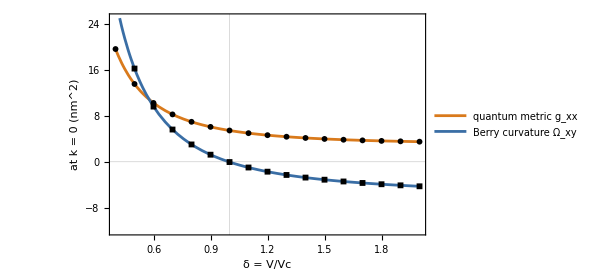

```mathematica
Show[
 Plot[{gClosed[del Vc], omClosed[del Vc]}, {del, 0.4, 2}, PlotRange -> {-12, 25},
  PlotStyle -> {Directive[cOrange, Thick], Directive[cBlue, Thick]},
  Frame -> True, FrameLabel -> {"δ = V/Vc", "at k = 0 (nm^2)"},
  GridLines -> {{1}, {0}}, PlotLegends -> {"quantum metric g_xx", "Berry curvature Ω_xy"},
  ImageSize -> 450],
 ListPlot[{Table[{del, geometry[0, 0, del Vc][[1]]}, {del, 0.4, 2, 0.1}],
   Table[{del, geometry[0, 0, del Vc][[2]]}, {del, 0.4, 2, 0.1}]},
  PlotStyle -> Black, PlotMarkers -> {Automatic, 6}]]
```

Message. At V_c the band carries a large quantum metric, g = 5.44 nm^2, half of it from the remote dimer bands, and almost no Berry curvature (Ω changes sign at V = 0.995 V_c). The geometry of the monkey saddle is metric dominated, and the metric is exactly what enters the GES.

## 4. Generalized electric susceptibility

### 4.1 Definition and decomposition

Bare spin susceptibility, per spin and valley, with k_± = k ± q/2:

χ^0(q) = - ∑_(n m) ∫ (d^2 k)/(2π)^2 (f(ε_(n,k_-)) - f(ε_(m,k_+)))/(ε_(n,k_-) - ε_(m,k_+)) |⟨ u_(n,k_-) | u_(m,k_+) ⟩|^2

The GES is its curvature at the origin:

χ_e ≡ ∂_q_x^2 χ^0(q) |_(q=0) ,    χ^0(q) ≃ χ^0(0) (1 - ℓ^2 q^2) ,    ℓ^2 = - χ_e/(2 χ^0(0))

A negative χ_e means q = 0 is a maximum of χ^0. Within RPA the Stoner instability then appears first in the uniform channel: the paramagnet has ferromagnetic fluctuations. Expanding to order q^2 gives χ_e = χ_geom + χ_mass with

χ_geom = 2 ∑_n ∫ (d^2 k)/(2π)^2 [ (f'(ε_n))/2 g_K^n + f(ε_n) X_n ] ,    χ_mass = -2 ∑_n ∫ (d^2 k)/(2π)^2 (f''(ε_n))/12 m_n^-1

g_K^n = ∑_(m ≠ n) (|v_nm^x|^2 + |v_nm^y|^2)/(ε_n - ε_m)^2 ,    X_n = ∑_(m ≠ n) (|v_nm^x|^2 + |v_nm^y|^2)/((ε_m - ε_n)(ε_n - ε_m)^2) ,    m_n^-1 = ∑_(m ≠ n) (|v_nm^x|^2 + |v_nm^y|^2)/(ε_n - ε_m)

Two observations organise everything that follows:

The Fermi-surface metric term is always negative because f' ≤ 0. Geometry always pushes towards ferromagnetism at the Fermi surface; the Fermi-sea term X_n can partly compensate.

f''(ε - μ) is odd about μ, so χ_mass measures the imbalance of band curvature just below and just above μ. Near a saddle it is large and changes sign as μ crosses E_vhs.

We call a ferromagnetic fluctuation geometry driven when χ_e < 0 but χ_mass > 0: the dispersion alone would make q = 0 a minimum.

### 4.2 Numerical method

Gauss–Legendre nodes. The radial integrals use 64-point Gauss–Legendre panels. Nodes and weights come from the eigenvalues and eigenvectors of the Jacobi matrix (Golub–Welsch), mapped to the interval [0, 1].

```mathematica
ngl = 64;
beta = Table[n/Sqrt[4. n^2 - 1], {n, 1, ngl - 1}];
jac = Table[If[Abs[i - j] == 1, beta[[Min[i, j]]], 0.], {i, ngl}, {j, ngl}];
{xgl, vgl} = Eigensystem[jac];

xg = (xgl + 1)/2;          (* nodes on [0, 1] *)
wg = vgl[[All, 1]]^2;      (* weights on [0, 1] *)

{Total[wg], wg.xg^2, wg.xg^9}     (* should be 1, 1/3, 1/10 *)
```

{1.,0.333333,0.1}

Polar grid. The integrands have the C_3 and mirror symmetry of the band, so it is enough to integrate over the 60° wedge 0 < φ < π/3 and multiply by six. The function below builds a polar grid on any wedge and scales the weights so that they cover the whole plane, including the measure d^2 k/(2π)^2.

```mathematica
polarGrid[edges_, nphi_, phimax_] := Module[{kr, wr, phis},
  kr = Flatten[Table[edges[[i]] + (edges[[i + 1]] - edges[[i]]) xg, {i, Length[edges] - 1}]];
  wr = Flatten[Table[(edges[[i + 1]] - edges[[i]]) wg, {i, Length[edges] - 1}]];
  phis = Table[(j - 0.5) phimax/nphi, {j, nphi}];
  {Flatten[Outer[Times, kr, Cos[phis]]],
   Flatten[Outer[Times, kr, Sin[phis]]],
   Flatten[Outer[Times, wr kr, Table[2 Pi/nphi, {nphi}]]]/(4 Pi^2)}]

(* inner grid: 12 panels up to 0.36 and 4 more up to 0.60 nm^-1, 48 angles in the wedge *)
edges = Join[Table[0.03 i, {i, 0, 12}], Table[0.36 + 0.06 i, {i, 1, 4}]];
{kxs, kys, ws} = polarGrid[edges, 48, Pi/3];

{Length[kxs], Total[ws] 4 Pi, 0.6^2}     (* number of points; area check: the last two agree *)
```

{49152,0.36,0.36}

Band data at one k point. For each of the four bands: energy, g_K, X and inverse mass, straight from the formulas of Section 4.1.

```mathematica
bandData[kx_, ky_, V_] := Module[{e, U, vx, vy, vv, de},
  {e, U} = bands[kx, ky, V];
  vx = Conjugate[U].dHx.Transpose[U];
  vy = Conjugate[U].dHy.Transpose[U];
  vv = Abs[vx]^2 + Abs[vy]^2;
  de = Table[If[n == m, 10.^15, e[[n]] - e[[m]]], {n, 4}, {m, 4}];    (* 10^15 removes m = n *)
  {e, Total[vv/de^2, {2}], Total[-vv/de^3, {2}], Total[vv/de, {2}]}]

bandData[0.05, 0.02, Vc] // TableForm
```

-0.403637 | -0.0200146 | 0.0200146 | 0.403637
5.23734 | 26.6861 | 26.6861 | 5.23734
13.0791 | 533.734 | -533.734 | -13.0791
-2.10641 | -0.645588 | 0.645588 | 2.10641

Tail. Beyond 0.6 nm^-1 there is no Fermi surface for the μ and T used here, so only the Fermi-sea term of the two filled valence bands survives. It decays slowly, so we integrate it on logarithmic panels up to k_max = 20 and 80 nm^-1 and extrapolate linearly in 1/k_max.

```mathematica
tail[V_, kmax_] := Module[{ed, kx, ky, w, xx},
  ed = Table[0.6 (kmax/0.6)^(i/16.), {i, 0, 16}];
  {kx, ky, w} = polarGrid[ed, 8, Pi/3];
  xx = Table[bandData[kx[[i]], ky[[i]], V][[3]], {i, Length[kx]}];
  2 w.(xx[[All, 1]] + xx[[All, 2]])]

prepare[del_] := Module[{V = del Vc, dat, out},
  dat = Table[bandData[kxs[[i]], kys[[i]], V], {i, Length[kxs]}];
  dat = Developer`ToPackedArray[dat];      (* packed storage keeps the later sums fast *)
  out = (80 tail[V, 80.] - 20 tail[V, 20.])/60;
  {dat[[All, 1]], dat[[All, 2]], dat[[All, 3]], dat[[All, 4]], out}]
```

Now tabulate the band data once for each bias used in the talk. This is the slow cell (about 50 000 diagonalisations per bias).

```mathematica
(* slow cell: expect something like 10 to 60 seconds per bias *)
AbsoluteTiming[
 Do[data[del] = prepare[del], {del, {0.5, 0.8, 1.0, 1.2, 1.5}}]]
```

{35.2449,Null}

The GES. With the band data stored, every (μ, T) point is just a weighted sum. The Fermi function is written with Tanh so that it never overflows; f' = -f(1-f)/T and f'' = f(1-f)(1-2f)/T^2. All four bands are kept with full Fermi functions.

```mathematica
(* returns {chi_geom, chi_mass, chi_e, chi0(q=0)};  dmu = mu - V/2 and T in meV *)
ges[del_, dmu_, T_] := Module[{en, gk, xs, ms, out, mu, t, f, fp, fpp, metric, shift, mass},
  {en, gk, xs, ms, out} = data[del];
  mu = del Vc/2 + 0.001 dmu;
  t = 0.001 T;
  f = (1 - Tanh[(en - mu)/(2 t)])/2;
  fp = -f (1 - f)/t;
  fpp = f (1 - f) (1 - 2 f)/t^2;
  metric = 2 ws.Total[fp gk/2, {2}];
  shift = 2 ws.Total[f xs, {2}] + out;
  mass = -2 ws.Total[fpp ms/12, {2}];
  {metric + shift, mass, metric + shift + mass, ws.Total[-fp, {2}]}]
```

Check at μ = V/2, T = 0.1  meV. Reference values: δ = 0.8: -16.91, 20.53, 3.63, 0.5727; δ = 1: -14.24, 25.82, 11.57, 0.6418; δ = 1.2: -12.64, 20.17, 7.53, 0.7000.

```mathematica
TableForm[
 Table[Prepend[ges[del, 0, 0.1], del], {del, {0.8, 1.0, 1.2}}],
 TableHeadings -> {None, {"δ", "χgeom (1/eV)", "χmass (1/eV)", "χe (1/eV)", "χ0(0) (1/eV nm^2)"}}]
```

δ | χgeom (1/eV) | χmass (1/eV) | χe (1/eV) | χ0(0) (1/eV nm^2)
0.8 | -16.9055 | 20.5342 | 3.6287 | 0.572719
1. | -14.2437 | 25.8177 | 11.574 | 0.641807
1.2 | -12.6361 | 20.169 | 7.53288 | 0.700034

## 5. Results

### 5.1 Dependence on chemical potential (Fig. 3)

The three components against μ at T = 0.1  meV for δ = 0.8, 1, 1.2. Top row: near the van Hove energy (dashed vertical line). Bottom row: the high-density side. Shading marks χ_e < 0: orange where the ferromagnetic fluctuation is geometry driven (χ_mass > 0), grey where it is dispersion driven.

```mathematica
cShadeGeo = RGBColor[0.965, 0.788, 0.541];
cShadeDisp = RGBColor[0.851, 0.784, 0.706];

muPanel[del_, mus_, yr_, vline_] := Module[{s, dm, shade},
  s = Table[ges[del, m, 0.1], {m, mus}];
  dm = mus[[2]] - mus[[1]];
  shade = Table[
    If[s[[i, 3]] < 0,
     {If[s[[i, 2]] > 0, cShadeGeo, cShadeDisp],
      Rectangle[{mus[[i]] - dm/2, yr[[1]]}, {mus[[i]] + dm/2, yr[[2]]}]},
     {}], {i, Length[mus]}];
  ListLinePlot[{Transpose[{mus, s[[All, 1]]}], Transpose[{mus, s[[All, 2]]}],
    Transpose[{mus, s[[All, 3]]}]},
   PlotStyle -> {Directive[cOrange, Thickness[0.006]],
     Directive[cBrown, Thickness[0.006], Dashed], Directive[Black, Thickness[0.009]]},
   PlotRange -> {{First[mus], Last[mus]}, yr}, Prolog -> shade,
   Frame -> True, Axes -> False,
   GridLines -> {vline, {0}}, GridLinesStyle -> Directive[Gray, Dashed],
   PlotLabel -> Row[{"V = ", del, " Vc"}],
   FrameLabel -> {"μ - V/2 (meV)", "GES (1/eV)"}, AspectRatio -> 0.8]]
```

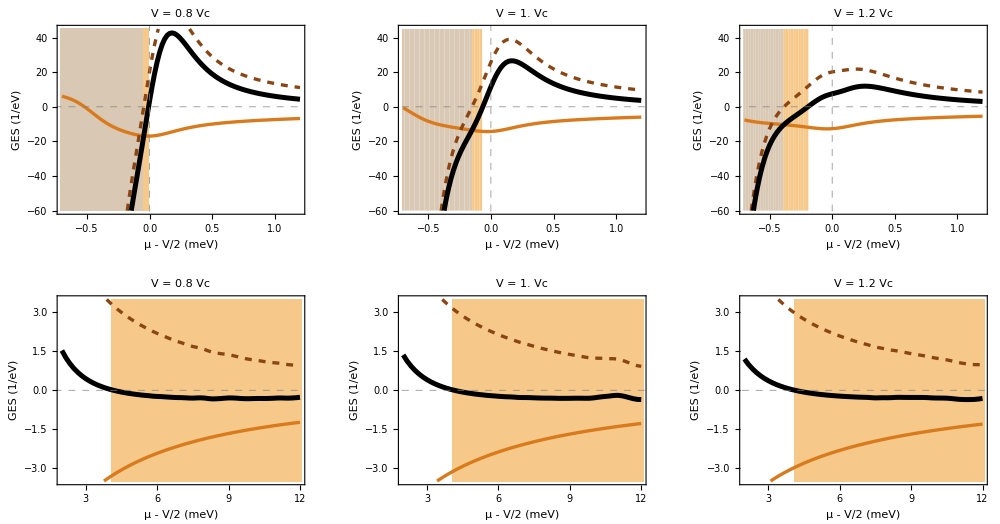

```mathematica
muNear = Table[-0.7 + 0.02 i, {i, 0, 95}];
muHigh = Table[2. + i/6., {i, 0, 60}];

top = Table[muPanel[del, muNear, {-60, 45}, {evhs[del]}], {del, {0.8, 1.0, 1.2}}];
bottom = Table[muPanel[del, muHigh, {-3.5, 3.5}, {}], {del, {0.8, 1.0, 1.2}}];

Column[{
  GraphicsGrid[{top, bottom}, ImageSize -> 1000],
  Row[{
    LineLegend[{Directive[cOrange, Thick], Directive[cBrown, Thick, Dashed], Directive[Black, Thick]},
     {Subscript["χ", "geom"], Subscript["χ", "mass"],
      Row[{Subscript["χ", "e"], " = ", Subscript["χ", "geom"], " + ", Subscript["χ", "mass"]}]},
     LegendLayout -> "Row"],
    SwatchLegend[{cShadeGeo, cShadeDisp}, {"FM, geometry-driven", "FM, dispersion-driven"},
     LegendLayout -> "Row"]}, Spacer[25]]},
 Alignment -> Center]
```

Near the van Hove energy both components are tens of eV^-1. χ_mass changes sign at E_vhs and controls the sign of χ_e. The ferromagnetic window just below E_vhs is mostly dispersion driven; geometry only widens it by the thin orange strip at its upper edge.

High-density side. The components are ten times smaller. χ_mass stays positive, χ_geom is negative and larger: from μ - V/2 ≈ 4.2  meV upward χ_e < 0 purely because of geometry, at all three biases.

### 5.2 Temperature dependence at the van Hove energy (Fig. 4)

The three components at μ = E_vhs for the three saddle phases δ = 0.5, 1, 1.5, from 0.1 to 10 meV, i.e. 1.16 to 116 K. Over this range the thermal window reaches the valence band, only V away, which is why all four bands carry full Fermi functions.

```mathematica
kB = 0.0861733;                                (* meV per kelvin *)
Tlist = Table[0.1*100^(i/23.), {i, 0, 23}];    (* 0.1 to 10 meV *)

Do[With[{ev = evhs[del]},
  tscan[del] = Table[ges[del, ev, T], {T, Tlist}]], {del, {0.5, 1.0, 1.5}}]

tempPlot[j_, name_] := ListLogLinearPlot[
  Table[Transpose[{Tlist/kB, tscan[del][[All, j]]}], {del, {0.5, 1.0, 1.5}}],
  Joined -> True, PlotMarkers -> Automatic,
  PlotStyle -> {Directive[cBlue, Thick], Directive[cBrown, Thick], Directive[cOrange, Thick]},
  Frame -> True, Axes -> False, GridLines -> {None, {0}}, PlotRange -> All,
  FrameLabel -> {"T (K)", Row[{name, " (", Superscript["eV", -1], ")"}]},
  PlotLabel -> Row[{name, " at μ = ", Subscript["E", "vhs"]}],
  PlotLegends -> Placed[{"δ = V/Vc = 0.5", "δ = V/Vc = 1.0", "δ = V/Vc = 1.5"}, {Right, Bottom}],
  ImageSize -> 520]
```

(a) χ_geom

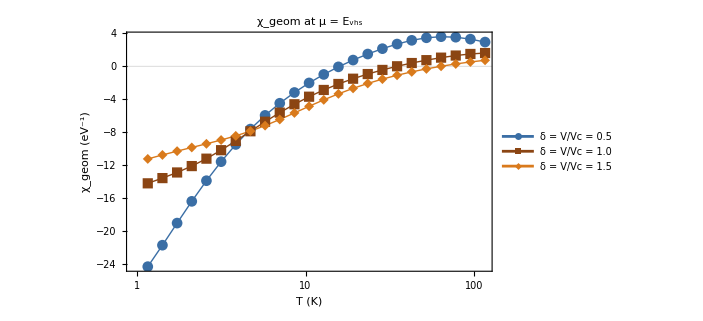

```mathematica
tempPlot[1, Subscript["χ", "geom"]]
```

(b) χ_mass

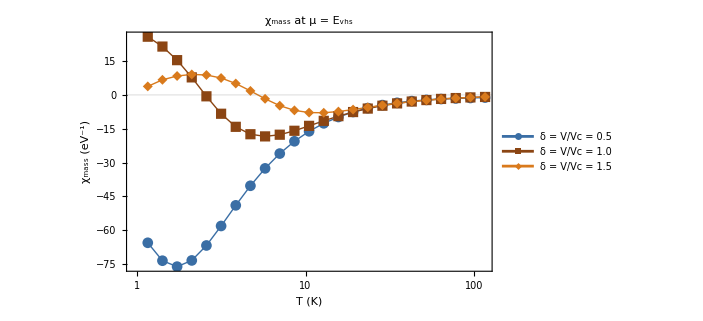

```mathematica
tempPlot[2, Subscript["χ", "mass"]]
```

(c) χ_e = χ_geom + χ_mass

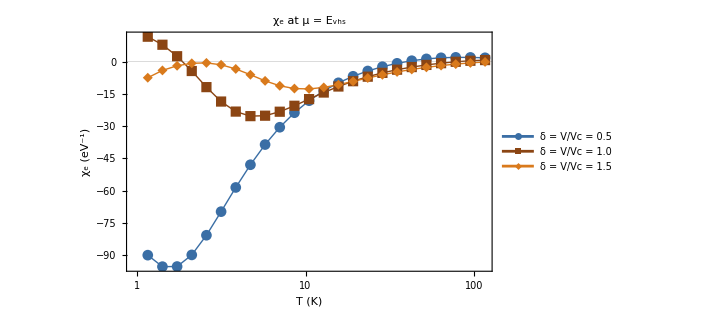

```mathematica
tempPlot[3, Subscript["χ", "e"]]
```

δ = 0.5. χ_mass is large and negative at all temperatures (minimum about -65 eV^-1 near 2 K), χ_e reaches -83 eV^-1. Strong ferromagnetic tendency, entirely dispersion driven.

δ = 1. At the lowest temperature χ_mass = +26 outweighs χ_geom = -14, so χ_e > 0. χ_mass changes sign near 2.5 K; geometry decides the sign only in a narrow interval around 2 K.

δ = 1.5. χ_e is negative over the whole range. Below about 5 K, χ_mass > 0 while χ_e < 0: above V_c the low-temperature ferromagnetic tendency is geometry driven.

In all three cases χ_geom turns positive at high temperature (near 16, 34 and 63 K), because thermal occupation of the valence band makes the positive Fermi-sea term dominate.

### 5.3 Strength and robustness (Fig. 5)

(a) At the van Hove energy the uniform susceptibility χ^0(0) should follow the T^(-1/3) law of the monkey saddle. (b) At μ - V/2 = 8  meV, deep in the high-density window, the full χ_e is compared with the dispersion-only value χ_mass.

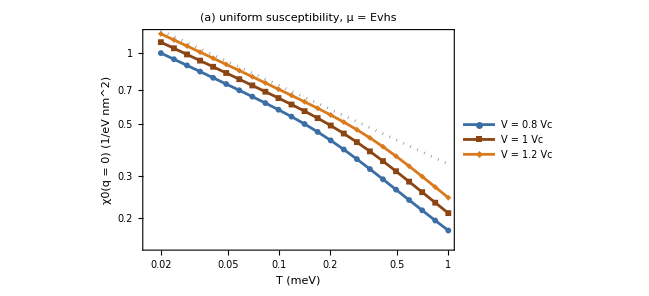
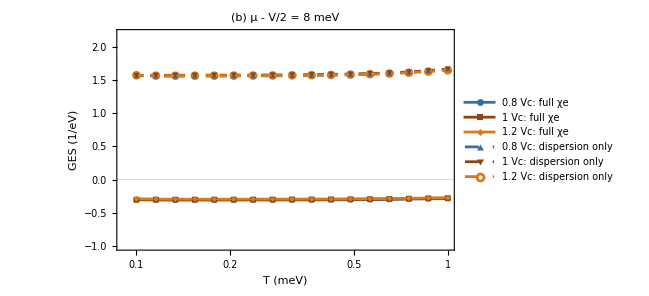

```mathematica
Tlow = Table[0.02*50^(i/22.), {i, 0, 22}];      (* 0.02 to 1 meV *)
Thigh = Table[0.1*10^(i/16.), {i, 0, 16}];      (* 0.1 to 1 meV *)

chi0curves = Table[
   With[{ev = evhs[del]}, Table[{T, ges[del, ev, T][[4]]}, {T, Tlow}]], {del, {0.8, 1.0, 1.2}}];
nu0 = ges[1.0, 0, 0.02][[4]];

figA = Show[

   ListLogLogPlot[chi0curves, Joined -> True, PlotMarkers -> {Automatic, 6},
    PlotStyle -> biasColors, Frame -> True,
    FrameLabel -> {"T (meV)", "χ0(q = 0)  (1/eV nm^2)"},
    PlotLabel -> "(a) uniform susceptibility, μ = Evhs",
    PlotLegends -> Placed[{"V = 0.8 Vc", "V = 1 Vc", "V = 1.2 Vc"}, {Right, Top}],
    ImageSize -> 480],
   LogLogPlot[1.12 nu0 (T/0.02)^(-1/3), {T, 0.02, 1}, PlotStyle -> Directive[Gray, Dotted]]];

ges8 = Table[Table[ges[del, 8, T], {T, Thigh}], {del, {0.8, 1.0, 1.2}}];

figB = ListLogLinearPlot[
   Join[Table[Transpose[{Thigh, ges8[[j, All, 3]]}], {j, 3}],
    Table[Transpose[{Thigh, ges8[[j, All, 2]]}], {j, 3}]],
   Joined -> True, PlotMarkers -> {Automatic, 6},
   PlotStyle -> Join[biasColors, Table[Directive[c, Dashed], {c, biasColors}]],
   PlotRange -> {-1, 2.2}, Frame -> True, Axes -> False, GridLines -> {None, {0}},
   FrameLabel -> {"T (meV)", "GES (1/eV)"}, PlotLabel -> "(b) μ - V/2 = 8 meV",
   PlotLegends -> {"0.8 Vc: full χe", "1 Vc: full χe", "1.2 Vc: full χe",
     "0.8 Vc: dispersion only", "1 Vc: dispersion only", "1.2 Vc: dispersion only"},
   ImageSize -> 480];

Row[{figA, figB}]
```

The dotted line in (a) is ∝ T^(-1/3). The analytic result for the pure cubic saddle is χ^0(0) ≃ 0.0702 A^(-2/3) T^(-1/3); the prefactor is a product of a Beta function (density of states) and a thermal integral. Compare with the four-band numbers:

```mathematica
pref = N[Beta[1/2, 1/6]/(12 Pi^2) * 2 (2^(4/3) - 1) Gamma[2/3] Abs[Zeta[-1/3]]]

TableForm[
 Table[{T, pref A3^(-2/3) (0.001 T)^(-1/3), ges[1.0, 0, T][[4]]}, {T, {0.02, 0.05, 0.1}}],
 TableHeadings -> {None, {"T (meV)", "analytic", "four-band"}}]
```

0.0702276-8.6004×10^-18 ⅈ

T (meV) | analytic | four-band
0.02 | 1.10944-1.35868×10^-16 ⅈ | 1.1113
0.05 | 0.817446-1.00108×10^-16 ⅈ | 0.814896
0.1 | 0.648807-7.9456×10^-17 ⅈ | 0.641807

Peak sharpness ℓ^2 = -χ_e / 2 χ^0(0) at μ - V/2 = 8  meV, T = 0.1  meV: geometry turns a dip of the bubble at q = 0 (negative ℓ^2) into a peak.

```mathematica
TableForm[
 Table[With[{s = ges[del, 8, 0.1]},
   {del, s[[3]], s[[2]], -s[[3]]/(2 s[[4]]), -s[[2]]/(2 s[[4]])}], {del, {0.8, 1.0, 1.2}}],
 TableHeadings -> {None, {"δ", "χe", "χmass", "ℓ^2 full (nm^2)", "ℓ^2 dispersion only (nm^2)"}}]
```

δ | χe | χmass | ℓ^2 full (nm^2) | ℓ^2 dispersion only (nm^2)
0.8 | -0.301929 | 1.56844 | 1.40397 | -7.29323
1. | -0.30349 | 1.57337 | 1.31701 | -6.82775
1.2 | -0.288881 | 1.57424 | 1.1792 | -6.42596

### 5.4 Direct test at finite q (Fig. 6)

The GES is a statement about the curvature of χ^0(q) at the origin. To test both the decomposition and its meaning we evaluate the bubble directly at finite q along x, for V = V_c, μ - V/2 = 8  meV and T = 0.2  meV, in two models:

the full four-band model;

the geometrically trivial model: same band energies, overlaps replaced by δ_nm, so that χ_geom = 0 by construction.

With q along x only the mirror k_y → -k_y survives, so the grid covers the upper half plane. Degenerate pairs use the limit -f'.

```mathematica
fermi[e_, mu_, t_] := (1 - Tanh[(e - mu)/(2 t)])/2

(* contribution of one k point: {full model, geometrically trivial model} *)
bubblePoint[kx_, ky_, q_, V_, mu_, t_] := Module[{em, um, ep, up, ov, fa, fb, ff},
  {em, um} = bands[kx - q/2, ky, V];
  {ep, up} = bands[kx + q/2, ky, V];
  ov = Abs[Conjugate[um].Transpose[up]]^2;       (* |<u_n,k-|u_m,k+>|^2 *)
  fa = fermi[em, mu, t];
  fb = fermi[ep, mu, t];
  ff = Table[
    If[Abs[em[[n]] - ep[[m]]] < 10.^-9,
     fa[[n]] (1 - fa[[n]])/t,
     -(fa[[n]] - fb[[m]])/(em[[n]] - ep[[m]])], {n, 4}, {m, 4}];
  {Total[ff ov, 2], Tr[ff]}]

(* half-plane grids: inner part up to 0.45 nm^-1, logarithmic outer part up to 40 nm^-1 *)
{kxIn, kyIn, wIn} = polarGrid[Table[0.45 i/8, {i, 0, 8}], 24, Pi];
{kxOut, kyOut, wOut} = polarGrid[Table[0.45 (40/0.45)^(i/6.), {i, 0, 6}], 6, Pi];

muq = Vc/2 + 0.008;  tq = 0.0002;

chiq[q_] :=
 wIn.Table[bubblePoint[kxIn[[i]], kyIn[[i]], q, Vc, muq, tq], {i, Length[kxIn]}] +
  wOut.Table[bubblePoint[kxOut[[i]], kyOut[[i]], q, Vc, muq, tq], {i, Length[kxOut]}]
```

```mathematica
(* slowest cell of the notebook: 26 values of q, about 15 000 k points each (a few minutes) *)
qlist = Join[Table[0.01 i, {i, 0, 12}], Table[0.16 + 0.02 i, {i, 0, 12}]];
AbsoluteTiming[cq = Table[chiq[q], {q, qlist}];]
```

{69.651,Null}

Small-q curvature of the two bubbles (a fit in q^2 to the first five points) against the GES prediction, χ_e/2 for the full model and χ_mass/2 for the trivial one:

```mathematica
fitFull = Fit[Table[{qlist[[i]]^2, cq[[i, 1]]}, {i, 5}], {1, z, z^2}, z];
fitTriv = Fit[Table[{qlist[[i]]^2, cq[[i, 2]]}, {i, 5}], {1, z, z^2}, z];
s8 = ges[1.0, 8, 0.2];

TableForm[{{"full four-band", Coefficient[fitFull, z, 1], s8[[3]]/2},
  {"geometrically trivial", Coefficient[fitTriv, z, 1], s8[[2]]/2}},
 TableHeadings -> {None, {"model", "curvature of the bubble", "GES prediction"}}]
```

model | curvature of the bubble | GES prediction
full four-band | -0.152619 | -0.150932
geometrically trivial | 0.789815 | 0.78843

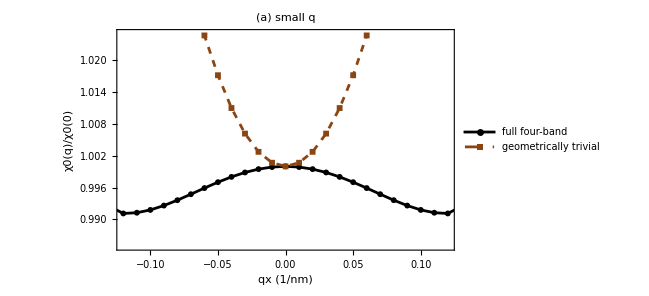
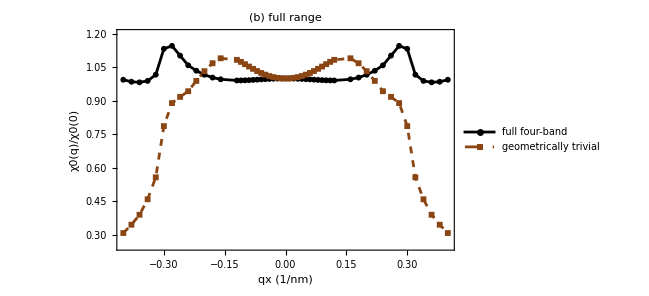

```mathematica
(* normalised curve chi0(q)/chi0(0), mirrored to negative q *)
sym[col_] := Module[{pts},
  pts = Table[{qlist[[i]], cq[[i, col]]/cq[[1, col]]}, {i, Length[qlist]}];
  Join[Reverse[Table[{-p[[1]], p[[2]]}, {p, Rest[pts]}]], pts]]

qPlot[qm_, yr_, title_] := ListLinePlot[{sym[1], sym[2]},
  PlotMarkers -> {Automatic, 6}, PlotStyle -> {Black, Directive[cBrown, Dashed]},
  PlotRange -> {{-qm, qm}, yr}, Frame -> True, Axes -> False,
  FrameLabel -> {"qx (1/nm)", "χ0(q)/χ0(0)"}, PlotLabel -> title,
  PlotLegends -> Placed[{"full four-band", "geometrically trivial"}, Below], ImageSize -> 480]

Row[{qPlot[0.12, {0.985, 1.025}, "(a) small q"], qPlot[0.40, {0.25, 1.2}, "(b) full range"]}]
```

```mathematica
(* position and height of the global maximum of the full bubble *)
Last[SortBy[Table[{qlist[[i]], cq[[i, 1]]/cq[[1, 1]]}, {i, Length[qlist]}], Last]]
```

(a) Small q. With geometry q = 0 is a maximum; without it, a minimum. The curvatures agree with χ_e/2 and χ_mass/2, an independent confirmation of the decomposition.

(b) Full range. The maximum at q = 0 is only local. The bubble has its global maximum at q ≈ 0.28 nm^-1, about 15% above χ^0(0). Within RPA an instability at this filling would first appear at finite wavevector.

### 5.5 Where ferromagnetic fluctuations live (Fig. 7)

Every point of the (μ, T) plane at V = V_c is classified by the signs of χ_e and χ_mass.

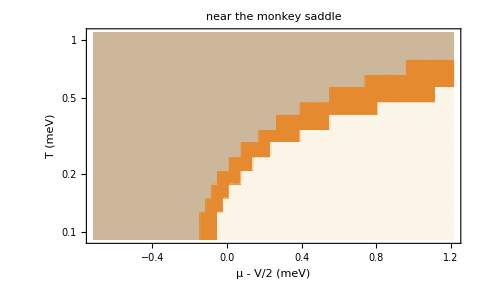
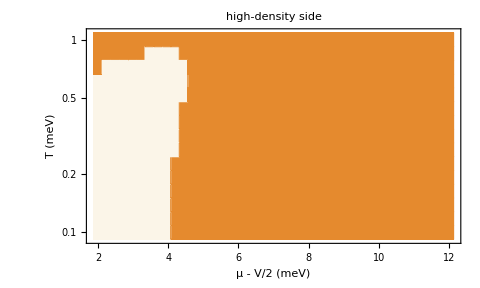

```mathematica
phaseColors = {RGBColor[0.984, 0.961, 0.910], RGBColor[0.804, 0.718, 0.604], RGBColor[0.898, 0.541, 0.180]};

(* 1: no FM fluctuation, 2: FM dispersion-driven, 3: FM geometry-driven *)
classify[del_, m_, T_] := Module[{s = ges[del, m, T]},
  Which[s[[3]] >= 0, 1, s[[2]] < 0, 2, True, 3]]

Tmap = Table[0.1*10^(i/14.), {i, 0, 14}];

phasePanel[mus_, title_] := Module[{dm, dl, col},
  dm = mus[[2]] - mus[[1]];
  dl = Log10[Tmap[[2]]/Tmap[[1]]];
  Graphics[
   Table[col = phaseColors[[classify[1.0, m, T]]];
    {col, EdgeForm[col],
     Rectangle[{m - dm/2, Log10[T] - dl/2}, {m + dm/2, Log10[T] + dl/2}]}, {T, Tmap}, {m, mus}],
   Frame -> True, AspectRatio -> 0.6, PlotLabel -> title,
   FrameLabel -> {"μ - V/2 (meV)", "T (meV)"},
   FrameTicks -> {{{{-1, "0.1"}, {Log10[0.2], "0.2"}, {Log10[0.5], "0.5"}, {0, "1"}}, None},
     {Automatic, None}}, ImageSize -> 480]]

Column[{
  Row[{phasePanel[Table[-0.7 + 1.9 i/60, {i, 0, 60}], "near the monkey saddle"],
    phasePanel[Table[2. + 10 i/41, {i, 0, 41}], "high-density side"]}],
  SwatchLegend[phaseColors,
   {"no FM fluctuation (χe > 0)", "FM, dispersion-driven", "FM, geometry-driven"},
   LegendLayout -> "Row"]}, Alignment -> Center]
```

Near the monkey saddle the dispersion-driven region dominates, and the geometry-driven region is a thin band along its boundary that moves to higher μ as T grows. On the high-density side the geometry-driven region is large and sharply bounded at μ - V/2 ≈ 4.2  meV.

## 6. Benchmark: the singular saddle point

As a check of the method we reproduce the setting of Kitamura et al.: a two-band model with a singular saddle at a quadratic band touching,

H(p) = p^2/(2 M) σ_0 + (p_x p_y)/M_xy σ_x + Δ σ_y + (p_x^2 - p_y^2)/(2 M_xx) σ_z ,    1/M = 1 ,    1/M_xx = 0.5 ,    1/M_xy = 1.5

At Δ = 0 the lower band has a singular saddle where the metric diverges as 1/p^2. A finite Δ opens a gap 2Δ, regularises the metric and splits the singularity into four ordinary saddles at energy E_s = -Δ √(1 - M_xy^2/M^2).

### 6.1 Bands (Fig. 8a)

```mathematica
pars = {1, 1/2, 3/2};       (* 1/M, 1/Mxx, 1/Mxy *)

(* s = +1 upper band, s = -1 lower band;  gp = Delta *)
eSing[s_, p_, q_, gp_] := pars[[1]] (p^2 + q^2)/2 +
  s Sqrt[(pars[[3]] p q)^2 + gp^2 + (pars[[2]] (p^2 - q^2)/2)^2]

eSaddle[gp_] := -gp Sqrt[1 - (pars[[1]]/pars[[3]])^2]
eSaddle[0.17]
```

-0.126711

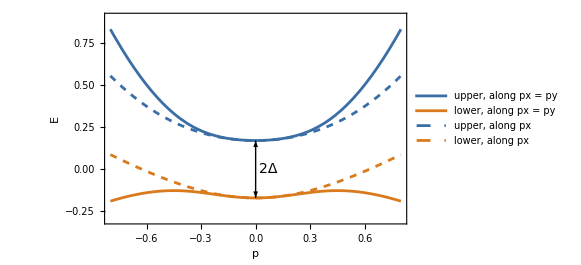
-Graphics3D--Graphics-

```mathematica
Row[{
  Plot3D[{eSing[1, p, q, 0.17], eSing[-1, p, q, 0.17]}, {p, -0.8, 0.8}, {q, -0.8, 0.8},
   PlotStyle -> {Directive[Opacity[0.6], RGBColor[0.6, 0.8, 1.]], Orange},
   AxesLabel -> {"px", "py", "E"}, ImageSize -> 430],
  Plot[{eSing[1, p/Sqrt[2], p/Sqrt[2], 0.17], eSing[-1, p/Sqrt[2], p/Sqrt[2], 0.17],
    eSing[1, p, 0, 0.17], eSing[-1, p, 0, 0.17]}, {p, -0.8, 0.8},
   PlotStyle -> {Directive[cBlue, Thick], Directive[cOrange, Thick],
     Directive[cBlue, Dashed], Directive[cOrange, Dashed]},
   PlotRange -> {-0.3, 0.9}, Frame -> True, FrameLabel -> {"p", "E"},
   Epilog -> {Arrowheads[{-0.03, 0.03}], Arrow[{{0, -0.17}, {0, 0.17}}],
     Text[Style["2Δ", 14], {0.07, 0}]},
   PlotLegends -> Placed[{"upper, along px = py", "lower, along px = py",
      "upper, along px", "lower, along px"}, {Left, Top}],
   ImageSize -> 430]}]
```

### 6.2 GES of the two-band model

For two bands everything is analytic. With h the vector multiplying the Pauli matrices and n = h/|h|: the metric is g_μν = ∂_μ n · ∂_ν n / 4 for both bands, so g_K = g_xx + g_yy; the Fermi-sea term is X = ± g_K / 2|h| (plus for the lower band); the inverse mass is half the Laplacian of the band energy. Mathematica takes the derivatives symbolically, then the expressions are evaluated on a polar grid over one quadrant with the momentum cutoff |p| ≤ 1.

```mathematica
hvec = {pars[[3]] px py, gap, pars[[2]] (px^2 - py^2)/2};
hn = Sqrt[hvec.hvec];
nvec = hvec/hn;

eUp = eSing[1, px, py, gap];
eDn = eSing[-1, px, py, gap];

gKs = (D[nvec, px].D[nvec, px] + D[nvec, py].D[nvec, py])/4;
mUp = (D[eUp, {px, 2}] + D[eUp, {py, 2}])/2;
mDn = (D[eDn, {px, 2}] + D[eDn, {py, 2}])/2;

Simplify[gKs /. gap -> 0]       (* the metric at band touching: diverges as 1/p^2 *)
```

(9 (px^2+py^2)^3)/((px^4+34 px^2 py^2+py^4)^2)

```mathematica
(* quadrant grid, 24 radial panels, 96 angles, cutoff |p| <= 1 *)
{pxs, pys, wps} = polarGrid[Table[i/24., {i, 0, 24}], 96, Pi/2];

(* band energies, masses, metric and |h| on the grid, stored for each gap *)
sing[gp_] := sing[gp] = ({eDn, eUp, mDn, mUp, gKs, hn} /. {px -> pxs, py -> pys, gap -> gp})

(* returns {chi_geom, chi_mass, chi_e} in model units *)
gesSing[gp_, T_, mu_] := Module[{ed, eu, md, mup, g, h, f, fp, fpp, geom = 0, mass = 0},
  {ed, eu, md, mup, g, h} = sing[gp];
  Do[
   f = (1 - Tanh[(b[[1]] - mu)/(2 T)])/2;
   fp = -f (1 - f)/T;
   fpp = f (1 - f) (1 - 2 f)/T^2;
   geom += 2 wps.(fp g/2 + f b[[3]]);
   mass += -2 wps.(fpp b[[2]]/12),
   {b, {{ed, md, g/(2 h)}, {eu, mup, -g/(2 h)}}}];
  {geom, mass, geom + mass}]

gesSing[0.17, 0.005, eSaddle[0.17]]     (* about {-0.73, 0.81, 0.09} *)
```

{-0.726553,0.813454,0.0869014}

### 6.3 Temperature dependence at the saddle energy (Fig. 8b)

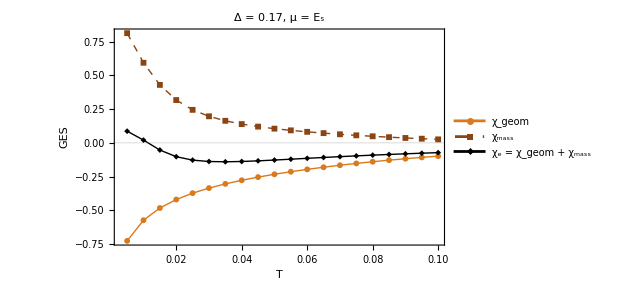
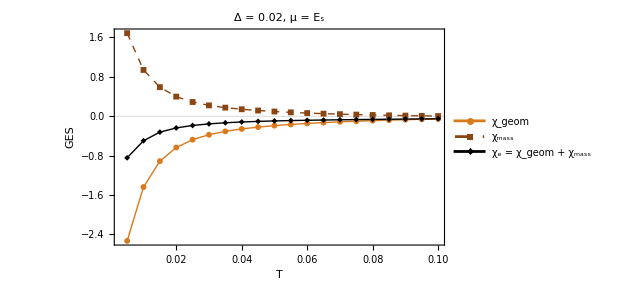

```mathematica
Tsing = Table[0.005 i, {i, 1, 20}];

singPlot[gp_] := Module[{s},
  s = Table[gesSing[gp, T, eSaddle[gp]], {T, Tsing}];
  ListLinePlot[Table[Transpose[{Tsing, s[[All, j]]}], {j, 3}],
   PlotMarkers -> {Automatic, 6},
   PlotStyle -> {Directive[cOrange, Thick], Directive[cBrown, Thick, Dashed], Directive[Black, Thick]},
   PlotRange -> All, Frame -> True, Axes -> False, GridLines -> {None, {0}},
   FrameLabel -> {"T", "GES"},
   PlotLabel -> Row[{"Δ = ", gp, ",  μ = ", Subscript["E", "s"]}],
   PlotLegends -> Placed[{Subscript["χ", "geom"], Subscript["χ", "mass"],
      Row[{Subscript["χ", "e"], " = ", Subscript["χ", "geom"], " + ", Subscript["χ", "mass"]}]},
     {Right, Bottom}],
   ImageSize -> 470]]

Row[{singPlot[0.17], singPlot[0.02]}]
```

The mass term is positive while χ_geom is negative and grows rapidly as the gap closes. For Δ = 0.17 the two nearly cancel and χ_e < 0 only above T ≈ 0.01. For Δ = 0.02, χ_e is clearly negative at all temperatures shown: the ferromagnetic tendency is geometry driven, as found by Kitamura et al.

### 6.4 Lifting the band touching

The same two bands as the gap parameter is varied; at zero the bands touch at the singular saddle. Drag the slider. (To explore another parameter set, change pars in Section 6.1 and re-evaluate this section.)

```mathematica
Manipulate[
 Plot3D[{eSing[1, p, q, dy], eSing[-1, p, q, dy]}, {p, -0.8, 0.8}, {q, -0.8, 0.8},
  PlotStyle -> {Directive[Blue, Opacity[0.8]], Directive[Red, Opacity[0.9]]},
  Mesh -> None, PlotRange -> {-0.5, 1.8}, ViewPoint -> {0, -3, 0.4},
  AxesLabel -> {"px", "py", "Energy"},
  PlotLabel -> Row[{"Degeneracy lifting: δy = ", NumberForm[dy, {4, 3}],
     "     Gap = ", NumberForm[2 dy, {4, 3}]}],
  ImageSize -> 500],
 {{dy, 0.17, "δy"}, 0, 0.3}]
```

Temperature scan exactly at band touching (Δ = 0, μ = 0). The only scale left is T, so each curve is close to 1/T:

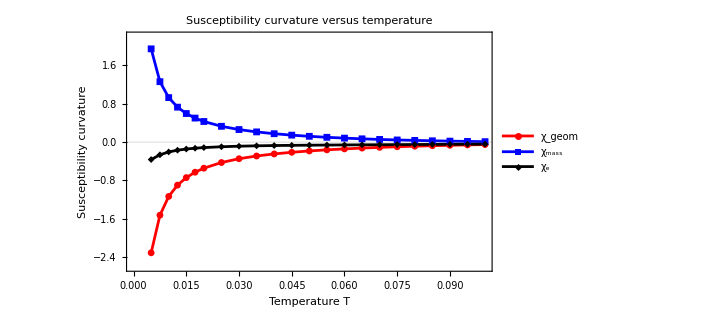

```mathematica
Ttouch = Join[{0.005, 0.0075, 0.01, 0.0125, 0.015, 0.0175}, Table[0.005 i, {i, 4, 20}]];
touch = Table[gesSing[0, T, 0], {T, Ttouch}];

ListLinePlot[{Transpose[{Ttouch, touch[[All, 1]]}], Transpose[{Ttouch, touch[[All, 2]]}],
  Transpose[{Ttouch, touch[[All, 3]]}]},
 PlotMarkers -> {Automatic, 7}, PlotStyle -> {Red, Blue, Black},
 PlotRange -> {-2.6, 2.2}, Frame -> True, Axes -> False, GridLines -> {None, {0}},
 FrameLabel -> {"Temperature T", "Susceptibility curvature"},
 PlotLabel -> "Susceptibility curvature versus temperature",
 PlotLegends -> {Subscript["χ", "geom"], Subscript["χ", "mass"], Subscript["χ", "e"]},
 ImageSize -> 520]
```

## 7. Conclusions

Geometry at the critical point. At V_c the two interband channels cancel in the effective mass and in the Berry curvature but add in the quantum metric. The monkey saddle carries a large, almost purely metric geometry: g ≃ 5.4 nm^2, Ω_xy ≈ 0.

Near the van Hove energy the dispersion controls the sign. χ_mass is large and changes sign at E_vhs; geometry only moves the edges of the ferromagnetic window.

Geometry-driven windows exist. On the high-density side, μ - V/2 ≳ 4.2  meV at all biases, and at low temperature at the van Hove energy for V > V_c, χ_e < 0 < χ_mass.

The maximum is local. In the geometry-driven window the global maximum of χ^0(q) sits at q ≈ 0.28 nm^-1, so an RPA instability there would first develop at finite wavevector.

Contrast with the singular saddle. There the metric diverges at a band touching and dominates. The monkey saddle is gapped, its metric stays finite, and geometry decides the sign only where the dispersion is nearly neutral.

### References

T. Kitamura, A. Daido and Y. Yanase, Spin-triplet superconductivity from quantum-geometry-induced ferromagnetic fluctuation, Phys. Rev. Lett. (2024); arXiv:2304.11536.

E. McCann and M. Koshino, The electronic properties of bilayer graphene, Rep. Prog. Phys. 76, 056503 (2013).

A. Shtyk, G. Goldstein and C. Chamon, Electrons at the monkey saddle: a multicritical Lifshitz point, Phys. Rev. B 95, 035137 (2017).

N. F. Q. Yuan, H. Isobe and L. Fu, Magic of high-order van Hove singularity, Nat. Commun. 10, 5769 (2019).

J. P. Provost and G. Vallee, Riemannian structure on manifolds of quantum states, Commun. Math. Phys. 76, 289 (1980).